```mathematica
matchCount[align_]:=StringLength[StringJoin@@Cases[align, _String]]
seqsim[seq1_, seq2_]:=matchCount[SequenceAlignment[EntityValue[seq1, "Sequence"], EntityValue[seq2, "Sequence"]]]
```

```mathematica
sample = EntityValue["Protein", "SampleEntities"];
```

```mathematica
labels=Labeled[ImageResize[EntityValue[#, "StructureDiagram"], {100,100}], #, ContentSize->{100,100}]&/@sample;
```

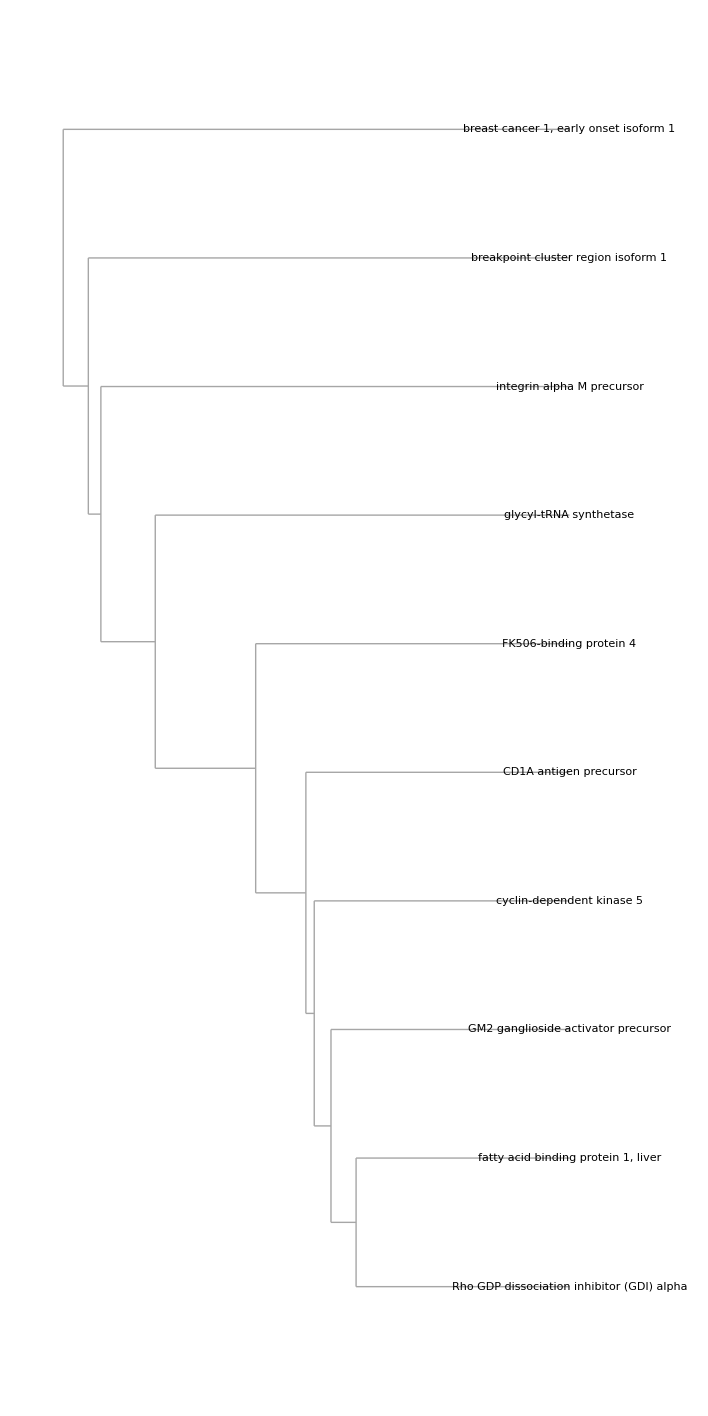

```mathematica
Dendrogram[sample->labels,Left,DistanceFunction->seqsim]
```